```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/PLTCM_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{3681,8,18000721-03000,327571,4,26,1222.64,4.48514,1.10517,1351.22,19.0359,1802.82,75.8486,120,2.68249,,0,,2,207254,0,678.897,1,1224.67,05.01.18 17:04,1.10509,0,NOOIL,,1,606,421,317,4.48514,1262.69,438.601,1222.64,1772}

{86222,38}

```mathematica
nullpos=Position[datafull[[All,9]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
mostlyzeropos=Join[Position[datafull[[All,12]],_?(#==0&)][[{2,3}]],
Position[datafull[[All,11]],_?(#==0&)][[{2,3}]]];
datafull=Delete[datafull,mostlyzeropos];
```

```mathematica
deletepos=Position[datafull[[All,9]],_?(100<#&)];
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos3=Position[datafull[[All,7]],_?(4000<#&)];
datafull=Delete[datafull,deletepos3];
```

```mathematica
deletepos2=Position[datafull[[All,7]],_?(100>#&)];
datafull=Delete[datafull,deletepos2];
```

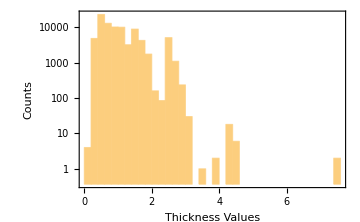
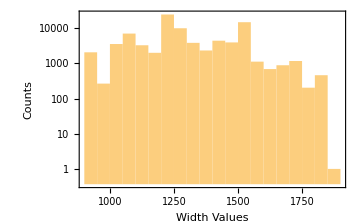

```mathematica
{Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,7]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafull[[Flatten@Position[datafull[[All,11]],_?Negative],11]]*=(-1);
```

```mathematica
datafull[[Flatten@Position[datafull[[All,12]],_?Negative],12]]*=(-1);
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,9]];
widthvaluesthkpos=datafull[[All,7]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|0.→23,2.62658×10^-10→1,7.59386×10^-10→1,7.67103×10^-10→1,1.47105×10^-9→1,2.03879×10^-9→1,84800,0.0557443→1,0.0564053→1,0.24686→3,0.287382→2,54.8716→1|>
 |  |  |  |

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(0<#<0.0001&)]]];
```

```mathematica
(* datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]]; *)
```

```mathematica
thickvaluesthkpos=datafull[[All,9]];
widthvaluesthkpos=datafull[[All,7]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

```mathematica
Length@densities
Length@Position[densities,_?(#≤6.5*10^(-6)&)]
Length@Position[densities,_?(8.5*10^(-6)≤#<0.0001&)]
```

84915

6042

10111

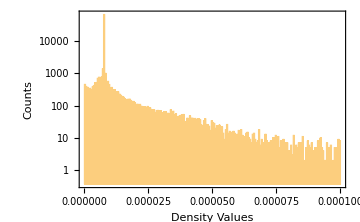

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
datafull=Delete[datafull,Position[datafull[[All,25]],""]];
```

```mathematica
datafullsorted=SortBy[datafull,AbsoluteTime[{#[[25]],{"Day",".","Month",".","YearShort"," ","Hour",":","Minute"}}]&];
```

```mathematica
differences=Differences[Table[AbsoluteTime[{datafullsorted[[i,25]],{"Day",".","Month",".","YearShort"," ","Hour",":","Minute"}}],{i,Length@datafullsorted}]]/3600.
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,84815,0.166667,0.1,0.1,0.1,0.1,0.166667,0.1,0.1,0.1,0.15,0.283333,0.366667,0.15,0.133333,0.15,0.133333,0.133333,0.133333,0.183333,0.133333,0.133333,0.133333,0.133333,0.133333,0.116667,0.133333,0.133333,0.133333,0.133333,0.1,0.1,0.116667,0.183333}
 |  |  |  |

```mathematica
Reverse@KeySort@Counts@differences;
```

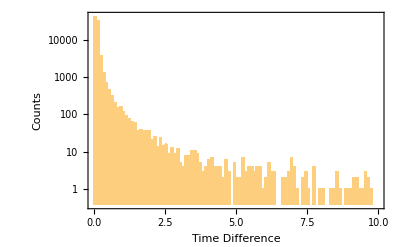

```mathematica
Histogram[differences,{10^-1},ScalingFunctions->"Log",PlotRange->{{0,10},All},Frame->True,FrameLabel->{"Time Difference","Counts"}]
```

```mathematica
Length@Position[differences,_?(#<0.5&)]
(Length@datafullsorted)-Length@Position[differences,_?(#<0.5&)]
```

82368

2514

```mathematica
pos=Flatten@Position[differences,_?(#≥0.5&)];
sequencecolumn=Flatten@Table[ConstantArray[i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{Range[Length@pos+1],Flatten@{First@pos,Table[{pos[[i+1]]-pos[[i]]},{i,Length@pos-1}],Length@datafullsorted-Last@pos}}]}];
```

```mathematica
Length@sequencecolumn
Length@DeleteDuplicates@sequencecolumn
Length@datafullsorted
```

84882

2514

84882

```mathematica
datafullsorted=Join[Partition[Range@Length@datafullsorted,1],Partition[sequencecolumn,1],datafullsorted,2];
```

```mathematica
(* checking if sequences are revealing consecutive *)
Length@Table[DeleteDuplicates@i,{i,Split[datafullsorted[[All,1]],#2==#1&]}]
Length@DeleteDuplicates[datafullsorted[[All,1]]]
```

84882

84882

```mathematica
datafullsorted[[1]]
```

{1,1,3811,7,18006201-06000,335622,4,26,1096.08,2.35629,0.4392,481.397,2.64984,480.605,79.6865,103.557,2.40365,,0,,2,207502,0,702.669,1,1098.11,01.01.01 00:00,0.43942,0,NOOIL,,1,622,421,317,2.35629,1137.37,1148.96,1094.58,6109}

```mathematica
data=Join[datafullsorted[[All,{1,2}]],ConstantArray[{0,0,0,0,0,0},Length@datafullsorted],datafullsorted[[All,{9,11,27}]],2];
```

```mathematica
Dimensions@data
```

{84882,11}

```mathematica
(* Export["pltcm_manipulated_84882.csv",data] *)
```